```mathematica
f1[x_,t_]:=Sin[x]*Cos[t]
```

```mathematica
f2[x_,t_]:=Sin[3*x]*Cos[9*t]
```



```mathematica
Plot[f1[x,0],{x,0,2*Pi}]
```

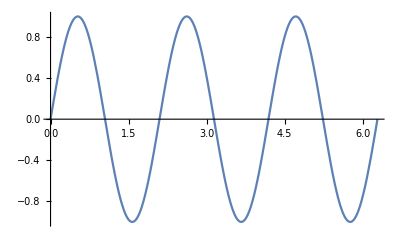

```mathematica
Plot[f2[x,0],{x,0,2*Pi}]
```

```mathematica
Animate[Plot[.5*f2[x,t]+f1[x,t],{x,0,2*Pi},PlotRange->{-2,2}],{t,0,2*Pi}]
```